### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =4;
d = 2;
lm = 1;
lp[k_]:=((k+1)^-(1/4))/lm;
$Assumptions = -1<k && Im[k]==0;
```

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*int1, int2, int3 and int4 are used for the normalization of the 2d 2par RDO*)
```

```mathematica
int1[ax_,bx_,ay_,by_]:=1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))));
int2[ax_,bx_,ay_,by_]:= 1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))));
int2[ax_,bx_,ay_,by_]:= 1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))));
int3[ax_,bx_,ay_,by_]:=1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))));
int4[ax_,bx_,ay_,by_]:= (3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)));
normpre[ax_,bx_, ay_, by_]:= 1/(int1[ax,bx,ay,by]+int2[ax,bx,ay,by]+int3[ax,bx,ay,by]+int4[ax,bx,ay,by]);
```

### Spin Components of the 2 particle RDO

```mathematica
(*the exponential contribution to the particle reduced density operator is determined analytically for the N-particle case as a polynomical (polyefunana with coefficient cp) and also written explicitly for the N=4 case in the efun function*)
```

```mathematica
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
polyefunana[a_,b_,Np_,x1_, x1p_, x2_, x2p_]:= (-a(x1^2+x2^2+x1p^2+x2p^2))+(b((x1+x2)^2+(x1p+x2p)^2))+(cp[a,b,Np]*(x1+x1p+x2+x2p)^2);
```

```mathematica
polyefunana[a,b,4,x1,x1p,x2,x2p]
```

(b^2 (x1+x1p+x2+x2p)^2)/(a-2 b)-a (x1^2+x1p^2+x2^2+x2p^2)+b ((x1+x2)^2+(x1p+x2p)^2)

```mathematica
efun[a_,b_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
```

```mathematica
(*rho2.. are the polynomial contributions to the 2particle reduced density operators in the various spin sectors. u <-> Up, d <-> Down. If only two spins are specified,e.g. uu then this is a diagonal entry,if 4 spins are specified this is an off-diagonal entry where the two first spins correspond to the ket and the two second spins to the bra, i.e. rho2uddu = ket(ud)*bra(du) *)
```

```mathematica
rho2dd[ax_,bx_, ay_, by_]:=(ax ay  π^2 (2 ay bx^2 (ay-2 by)^2 (y1p-y2p) (y1+y1p-y2-y2p)+2 ax^3 (2 by^2 (x1-x2) (x1p-x2p)+2 ay^3 (x2p y1p-x1p y2p) (x2 (y1+y1p)-x1 (y2+y2p))+ay by (x2 (3 x1p-3 x2p+by x2p (3 y1^2+18 y1 y1p+15 y1p^2+4 y1 (y2+y2p)+8 y1p (y2+y2p)+(y2+y2p)^2)-by x1p (3 y1^2+3 y1p^2+y2^2+6 y2 y2p+5 y2p^2+4 y1p (y2+4 y2p)+2 y1 (3 y1p+2 y2+8 y2p)))+x1 (-3 x1p+3 x2p-by x2p (y1^2+6 y1 y1p+5 y1p^2+4 y1 (y2+y2p)+16 y1p (y2+y2p)+3 (y2+y2p)^2)+by x1p (y1^2+y1p^2+4 y1p (y2+2 y2p)+2 y1 (y1p+2 y2+4 y2p)+3 (y2^2+6 y2 y2p+5 y2p^2))))+ay^2 (x1 (x1p-by x1p (y2^2+12 y2 y2p+11 y2p^2+y1 (y2+3 y2p)+y1p (y2+3 y2p))+x2p (-1+by (2 y1p^2+11 y1p (y2+y2p)+(y2+y2p)^2+y1 (2 y1p+y2+y2p))))+x2 (x2p-by x2p (y1^2+y1 (12 y1p+y2+y2p)+y1p (11 y1p+3 (y2+y2p)))+x1p (-1+by (y1^2+y1p^2+2 y2p (y2+y2p)+y1p (y2+11 y2p)+y1 (2 y1p+y2+11 y2p))))))+ax^2 (-16 bx by^2 (x1-x2) (x1p-x2p)+ay^3 ((1-2 bx (x2^2+10 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p))) y1p^2-(-1+2 bx (x1^2+x1p (x1p+x2+x2p)+x1 (10 x1p+x2+x2p))) y2p (y2+y2p)+y1 (y1p-2 bx (x2^2+10 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)) y1p+(-1+2 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p))) y2p)+y1p ((-1+2 bx (x1^2+x2p (x1p+x2+x2p)+x1 (x1p+x2+10 x2p))) y2+2 (-1+bx (x1^2+x1p^2+(x2+x2p)^2+2 x1p (5 x2+x2p)+2 x1 (x1p+x2+5 x2p))) y2p))-ay^2 (4 by (y1p-y2p) (y1+y1p-y2-y2p)+bx (8 x2 x2p-9 by x2 x2p y1^2-by x2p^2 y1^2-10 by x2^2 y1 y1p-116 by x2 x2p y1 y1p-10 by x2p^2 y1 y1p-10 by x2^2 y1p^2-107 by x2 x2p y1p^2-9 by x2p^2 y1p^2-8 by x2 x2p y1 y2-2 by x2^2 y1p y2-18 by x2 x2p y1p y2+8 by x2p^2 y1p y2+by x2 x2p y2^2+by x2p^2 y2^2+10 by x2^2 y1 y2p+2 by x2 x2p y1 y2p+8 by x2^2 y1p y2p-8 by x2 x2p y1p y2p+8 by x2p^2 y1p y2p+2 by x2^2 y2 y2p+4 by x2 x2p y2 y2p+2 by x2p^2 y2 y2p+2 by x2^2 y2p^2+3 by x2 x2p y2p^2+by x2p^2 y2p^2+2 by x1^2 (y1p-y2p) (y1+y1p+5 (y2+y2p))+by x1p^2 (y1^2+y1p^2-y2^2+8 y1p y2p-10 y2 y2p-9 y2p^2+2 y1 (y1p+4 y2p))+x1 (-8 by x2 (y1p-y2p) (y1+y1p-y2-y2p)+x1p (8+by (y1^2+4 y1 y1p+3 y1p^2-8 y1 y2+2 y1p y2-9 y2^2-18 y1 y2p-8 y1p y2p-116 y2 y2p-107 y2p^2))+x2p (-8+by (-y1^2+8 y1 y1p+9 y1p^2+8 y1 y2+106 y1p y2+9 y2^2+6 y1 y2p+104 y1p y2p+8 y2 y2p-y2p^2)))+x1p (-8 by x2p (y1p-y2p) (y1+y1p-y2-y2p)+x2 (-8+by (9 y1^2+8 y1 y1p-y1p^2+8 y1 y2+6 y1p y2-y2^2+106 y1 y2p+104 y1p y2p+8 y2 y2p+9 y2p^2)))))+2 ay by (2 by (y1p-y2p) (y1+y1p-y2-y2p)+bx (12 x2 x2p-13 by x2 x2p y1^2-by x2p^2 y1^2-6 by x2^2 y1 y1p-84 by x2 x2p y1 y1p-6 by x2p^2 y1 y1p-6 by x2^2 y1p^2-71 by x2 x2p y1p^2-5 by x2p^2 y1p^2-16 by x2 x2p y1 y2-2 by x2^2 y1p y2-30 by x2 x2p y1p y2+4 by x2p^2 y1p y2-3 by x2 x2p y2^2+by x2p^2 y2^2+6 by x2^2 y1 y2p-10 by x2 x2p y1 y2p+4 by x2^2 y1p y2p-24 by x2 x2p y1p y2p+4 by x2p^2 y1p y2p+2 by x2^2 y2 y2p-4 by x2 x2p y2 y2p+2 by x2p^2 y2 y2p+2 by x2^2 y2p^2-by x2 x2p y2p^2+by x2p^2 y2p^2+2 by x1^2 (y1p-y2p) (y1+y1p+3 (y2+y2p))+by x1p^2 (y1^2+y1p^2-y2^2+4 y1p y2p-6 y2 y2p-5 y2p^2+2 y1 (y1p+2 y2p))+x1p (-4 by x2p (y1p-y2p) (y1+y1p-y2-y2p)+x2 (-12+by (13 y1^2+20 y1 y1p+7 y1p^2+16 y1 y2+14 y1p y2+3 y2^2+74 y1 y2p+72 y1p y2p+20 y2 y2p+17 y2p^2)))-x1 (12 x2p+4 by x2 (y1p-y2p) (y1+y1p-y2-y2p)-by x2p (3 y1^2+17 y1p^2+74 y1p y2+13 y2^2+72 y1p y2p+20 y2 y2p+7 y2p^2+2 y1 (10 y1p+8 y2+7 y2p))+x1p (-12+by (3 y1^2+4 y1 y1p+y1p^2+16 y1 y2+10 y1p y2+13 y2^2+30 y1 y2p+24 y1p y2p+84 y2 y2p+71 y2p^2))))))+ax bx (16 bx by^2 (x1-x2) (x1p-x2p)+ay^3 ((-3+bx (x1^2+x1p^2+5 x2^2+26 x2 x2p+5 x2p^2+6 x1p (x2+x2p)+2 x1 (x1p+3 (x2+x2p)))) y1p^2+(-3+bx (5 x1^2+26 x1 x1p+5 x1p^2+6 x1 (x2+x2p)+6 x1p (x2+x2p)+(x2+x2p)^2)) y2p (y2+y2p)+y1 (-3 y1p+bx (x1^2+x1p^2+5 x2^2+26 x2 x2p+5 x2p^2+6 x1p (x2+x2p)+2 x1 (x1p+3 (x2+x2p))) y1p+3 y2p-bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p)) y2p)-y1p ((-3+bx (5 x1^2+x1p^2+2 x1p x2+x2^2+6 x1p x2p+6 x2 x2p+5 x2p^2+x1 (6 x1p+6 x2+26 x2p))) y2+2 (-3+bx (3 x1^2+3 x1p^2+3 (x2+x2p)^2+2 x1p (7 x2+3 x2p)+2 x1 (3 x1p+3 x2+7 x2p))) y2p))+2 ay^2 (6 by (y1p-y2p) (y1+y1p-y2-y2p)+bx (4 x2 x2p-5 by x2 x2p y1^2-by x2p^2 y1^2-12 by x2^2 y1 y1p-72 by x2 x2p y1 y1p-12 by x2p^2 y1 y1p-12 by x2^2 y1p^2-67 by x2 x2p y1p^2-11 by x2p^2 y1p^2-4 by x2 x2p y1 y2-2 by x2 x2p y1p y2+10 by x2p^2 y1p y2+by x2 x2p y2^2+by x2p^2 y2^2-12 by x1p x2p (y1p-y2p) (y1+y1p-y2-y2p)+12 by x2^2 y1 y2p+10 by x2 x2p y1 y2p+2 by x2p^2 y1 y2p+12 by x2^2 y1p y2p+12 by x2 x2p y1p y2p+12 by x2p^2 y1p y2p-by x2 x2p y2p^2-by x2p^2 y2p^2+12 by x1^2 (y1p-y2p) (y2+y2p)+by x1p^2 (y1^2-y1p^2-y2^2+10 y1 y2p-12 y2 y2p-11 y2p^2+2 y1p (y2+6 y2p))+x1p x2 (-4+by (5 y1^2-9 y1p^2+6 y1p y2-y2^2+68 y1p y2p-4 y2 y2p-3 y2p^2+y1 (-4 y1p+4 y2+66 y2p)))+x1 (-12 by x2 (y1p-y2p) (y1+y1p-y2-y2p)-x2p (4+by (y1^2+4 y1 y1p+3 y1p^2-4 y1 y2-66 y1p y2-5 y2^2-6 y1 y2p-68 y1p y2p+4 y2 y2p+9 y2p^2))+x1p (4+by (y1^2-y1p^2+10 y1p y2-5 y2^2+12 y1p y2p-72 y2 y2p-67 y2p^2-2 y1 (2 y2+y2p))))))-4 ay by (3 by (y1p-y2p) (y1+y1p-y2-y2p)+bx (6 x2 x2p-7 by x2 x2p y1^2-by x2p^2 y1^2-7 by x2^2 y1 y1p-50 by x2 x2p y1 y1p-7 by x2p^2 y1 y1p-7 by x2^2 y1p^2-43 by x2 x2p y1p^2-6 by x2p^2 y1p^2-8 by x2 x2p y1 y2-by x2^2 y1p y2-12 by x2 x2p y1p y2+5 by x2p^2 y1p y2-by x2 x2p y2^2+by x2p^2 y2^2-6 by x1p x2p (y1p-y2p) (y1+y1p-y2-y2p)+7 by x2^2 y1 y2p+by x2p^2 y1 y2p+6 by x2^2 y1p y2p-4 by x2 x2p y1p y2p+6 by x2p^2 y1p y2p+by x2^2 y2 y2p-2 by x2 x2p y2 y2p+by x2p^2 y2 y2p+by x2^2 y2p^2-by x2 x2p y2p^2+by x1p^2 (y1+y1p-y2-y2p) (y1+y2+6 y2p)+by x1^2 (y1p-y2p) (y1+y1p+7 (y2+y2p))+x1p x2 (-6+by (7 y1^2-y1p^2+8 y1p y2+y2^2+44 y1p y2p+6 y2 y2p+5 y2p^2+y1 (6 y1p+8 y2+44 y2p)))-x1 (6 x2p+6 by x2 (y1p-y2p) (y1+y1p-y2-y2p)-by x2p (y1^2+6 y1 y1p+5 y1p^2+7 y2^2+6 y2 y2p-y2p^2+8 y1 (y2+y2p)+44 y1p (y2+y2p))+x1p (-6+by (y1^2+y1p^2+7 y2^2+4 y1p y2p+50 y2 y2p+43 y2p^2+2 y1 (y1p+4 y2+6 y2p)))))))))/(((ax (ax-2 bx))/(ax-bx))^(5/2) (ax-bx)^(5/2) ((ay (ay-2 by))/(ay-by))^(5/2) (ay-by)^(5/2));
rho2ud[ax_,bx_, ay_, by_] := (ax ay  π^2 (4 ax^3 (ay-2 by)^2 x2 x2p+2 ay bx^2 (ay+8 ay^2 y2 y2p-4 ay by (y2^2+10 y2 y2p+y2p^2+y1 (y2+y2p)+y1p (y2+y2p))+2 by (-1+by (y1^2+y1p^2+5 y2^2+26 y2 y2p+5 y2p^2+6 y1p (y2+y2p)+2 y1 (y1p+3 (y2+y2p)))))+ax^2 (-2 by^2 (-1+4 bx (x2^2+10 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)))+4 ay^3 y2 y2p-ay^2 (-1+2 bx (x2^2+10 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p))+2 by (y2^2+10 y2 y2p+y2p^2+y1 (y2+y2p)+y1p (y2+y2p)))+ay by (-3+8 bx (x2^2+10 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p))+by (y1^2+y1p^2+5 y2^2+26 y2 y2p+5 y2p^2+6 y1p (y2+y2p)+2 y1 (y1p+3 (y2+y2p)))))+ax bx (4 by^2 (-1+bx (x1^2+x1p^2+5 x2^2+26 x2 x2p+5 x2p^2+6 x1p (x2+x2p)+2 x1 (x1p+3 (x2+x2p))))-16 ay^3 y2 y2p+ay^2 (-3+bx (x1^2+x1p^2+5 x2^2+26 x2 x2p+5 x2p^2+6 x1p (x2+x2p)+2 x1 (x1p+3 (x2+x2p)))+8 by (y2^2+10 y2 y2p+y2p^2+y1 (y2+y2p)+y1p (y2+y2p)))-4 ay by (-2+bx (x1^2+x1p^2+5 x2^2+26 x2 x2p+5 x2p^2+6 x1p (x2+x2p)+2 x1 (x1p+3 (x2+x2p)))+by (y1^2+y1p^2+5 y2^2+26 y2 y2p+5 y2p^2+6 y1p (y2+y2p)+2 y1 (y1p+3 (y2+y2p)))))))/(2 ((ax (ax-2 bx))/(ax-bx))^(5/2) (ax-bx)^(5/2) ((ay (ay-2 by))/(ay-by))^(5/2) (ay-by)^(5/2));
rho2du[ax_,bx_, ay_, by_]:=(ax ay  π^2 (4 ax^3 (ay-2 by)^2 x1 x1p+2 ay bx^2 (ay+8 ay^2 y1 y1p-4 ay by (y1^2+y1p (y1p+y2+y2p)+y1 (10 y1p+y2+y2p))+2 by (-1+by (5 y1^2+26 y1 y1p+5 y1p^2+6 y1 (y2+y2p)+6 y1p (y2+y2p)+(y2+y2p)^2)))+ax^2 (-2 by^2 (-1+4 bx (x1^2+x1p (x1p+x2+x2p)+x1 (10 x1p+x2+x2p)))+4 ay^3 y1 y1p+ay by (-3+8 bx (x1^2+x1p (x1p+x2+x2p)+x1 (10 x1p+x2+x2p))+by (5 y1^2+26 y1 y1p+5 y1p^2+6 y1 (y2+y2p)+6 y1p (y2+y2p)+(y2+y2p)^2))-ay^2 (-1+2 bx (x1^2+x1p (x1p+x2+x2p)+x1 (10 x1p+x2+x2p))+2 by (y1^2+y1p (y1p+y2+y2p)+y1 (10 y1p+y2+y2p))))+ax bx (4 by^2 (-1+bx (5 x1^2+26 x1 x1p+5 x1p^2+6 x1 (x2+x2p)+6 x1p (x2+x2p)+(x2+x2p)^2))-16 ay^3 y1 y1p-4 ay by (-2+bx (5 x1^2+26 x1 x1p+5 x1p^2+6 x1 (x2+x2p)+6 x1p (x2+x2p)+(x2+x2p)^2)+by (5 y1^2+26 y1 y1p+5 y1p^2+6 y1 (y2+y2p)+6 y1p (y2+y2p)+(y2+y2p)^2))+ay^2 (-3+bx (5 x1^2+26 x1 x1p+5 x1p^2+6 x1 (x2+x2p)+6 x1p (x2+x2p)+(x2+x2p)^2)+8 by (y1^2+y1p (y1p+y2+y2p)+y1 (10 y1p+y2+y2p))))))/(2 ((ax (ax-2 bx))/(ax-bx))^(5/2) (ax-bx)^(5/2) ((ay (ay-2 by))/(ay-by))^(5/2) (ay-by)^(5/2));
rho2uddu[ax_,bx_, ay_, by_]:=-((ax ay  π^2 (4 ax^3 (ay-2 by)^2 x1p x2+2 ay bx^2 (ay+8 ay^2 y1p y2-4 ay by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))+2 by (-1+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p))))+ax^2 (-2 by^2 (-1+4 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p)))+4 ay^3 y1p y2+ay by (-3+8 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p))+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p)))-ay^2 (-1+2 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p))+2 by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))))+ax bx (4 by^2 (-1+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p)))-16 ay^3 y1p y2-4 ay by (-2+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p))+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p)))+ay^2 (-3+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p))+8 by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))))))/(2 ((ax (ax-2 bx))/(ax-bx))^(5/2) (ax-bx)^(5/2) ((ay (ay-2 by))/(ay-by))^(5/2) (ay-by)^(5/2)));
rho2duud[ax_,bx_, ay_, by_]:=-((ax ay  π^2 (4 ax^3 (ay-2 by)^2 x1p x2+2 ay bx^2 (ay+8 ay^2 y1p y2-4 ay by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))+2 by (-1+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p))))+ax^2 (-2 by^2 (-1+4 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p)))+4 ay^3 y1p y2+ay by (-3+8 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p))+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p)))-ay^2 (-1+2 bx (x1p^2+x1 (x1p+x2)+x2 (x2+x2p)+x1p (10 x2+x2p))+2 by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))))+ax bx (4 by^2 (-1+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p)))-16 ay^3 y1p y2-4 ay by (-2+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p))+by (y1^2+5 y1p^2+26 y1p y2+5 y2^2+6 y1p y2p+6 y2 y2p+y2p^2+2 y1 (3 y1p+3 y2+y2p)))+ay^2 (-3+bx (x1^2+5 x1p^2+26 x1p x2+5 x2^2+6 x1p x2p+6 x2 x2p+x2p^2+2 x1 (3 x1p+3 x2+x2p))+8 by (y1p^2+y1 (y1p+y2)+y2 (y2+y2p)+y1p (10 y2+y2p))))))/(2 ((ax (ax-2 bx))/(ax-bx))^(5/2) (ax-bx)^(5/2) ((ay (ay-2 by))/(ay-by))^(5/2) (ay-by)^(5/2)));
```

```mathematica
(*define 2 particle hf basis*)
(*modes are always defined such that for multi spin basis m1 has spin UP and m2 has spin DOWN, the exponential factor of the Hermite function is included in the exppolyinit variable, here we are only interested in the polynomial contribution of the hf basis*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hfbasisud[m1_, m2_,a_, x1_, x2_]:=1/Sqrt[2](hfcoef[m1,x1,a]*hfcoef[m2,x2, a])
hfbasisdu[m1_, m2_,a_,  x1_, x2_]:=1/Sqrt[2](-hfcoef[m1,x2,a]*hfcoef[m2,x1, a])
hfbasis[m1_, m2_, a_, x1_, x2_]:=1/Sqrt[2]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2, a]}, {hfcoef[m2,x1,a],hfcoef[m2,x2, a]}}]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 2 - RDO

```mathematica
(*Determine the coefficients of the polynomial 'hfbasis' by the coefficientlist function where q corresponds to the power of the particular variable, i.e. x^q !NOTE! this is not the same as the index Mathematica gives the in the CoefficientList function, *)
```

```mathematica
(*polystart.. denotes the spin component of the polynomial which is comprised of the hermite basis functions and the polynomial contribution of the corresponding spin sector of the 2particle RDO. This is then used in the algorithm in "Running the algorithm" to calculates the integral which is a combination of a polynomial*gaussian exponential*)
```

```mathematica
polystartdd[mode1x_, mode2x_, mode1y_, mode2y_]:=hfbasis[mode1x,mode2x, ax, x1, x2]*hfbasis[mode1x,mode2x, ax, x1p, x2p]hfbasis[mode1y,mode2y, ay, y1, y2]*hfbasis[mode1y,mode2y, ay, y1p, y2p]*rho2dd[ax,bx,ay,by]
```

```mathematica
(*polystartuu[mode1_, mode2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[mode1,mode2, a, x1p, x2p]*rho2uu[a,b]*)
polystartud[mode1x_, mode2x_, mode1y_, mode2y_]:=hfbasisud[mode1x,mode2x, ax, x1, x2]*hfbasisud[mode1x,mode2x, ax, x1p, x2p]*hfbasisud[mode1y,mode2y, ay, y1, y2]*hfbasisud[mode1y,mode2y, ay, y1p, y2p]*rho2ud[ax,bx,ay,by]+hfbasisdu[mode1x,mode2x, ax, x1, x2]*hfbasisdu[mode1x,mode2x, ax, x1p, x2p]hfbasisdu[mode1y,mode2y, ay, y1, y2]*hfbasisdu[mode1y,mode2y, ay, y1p, y2p]*rho2du[ax,bx,ay,by]-hfbasisdu[mode1x,mode2x, ax, x1, x2]*hfbasisud[mode1x,mode2x, ax, x1p, x2p]*hfbasisdu[mode1y,mode2y, ay, y1, y2]*hfbasisud[mode1y,mode2y, ay, y1p, y2p]*rho2uddu[ax,bx,ay,by]-hfbasisud[mode1x,mode2x, ax, x1, x2]*hfbasisdu[mode1x,mode2x, ax, x1p, x2p]*hfbasisud[mode1y,mode2y, ay, y1, y2]*hfbasisdu[mode1y,mode2y, ay, y1p, y2p]*rho2duud[ax,bx,ay,by]
```

```mathematica
coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*sanity check to see whether coefficient decomposition works as expected*)
```

```mathematica
Sum[coefstart[polystartdd[5,4],x1,q]*x1^q,{q,0,maxdegreestart[polystartdd[5,4],x1]}]-polystartdd[5,4]//Simplify
```

0

### Integrating coefficient by coefficient, defining helper functions

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
(*exppolyinit is the initial polynomial of the Exp contribution to the 2-particle RDO*)
```

```mathematica
exppolyinit=-1/((ax-2 bx) (ay-2 by))(ax^2 (ay-2 by) (x1^2+x1p^2+x2^2+x2p^2)+bx (ay bx (x1-x1p+x2-x2p)^2-2 by (bx (x1-x1p+x2-x2p)^2+by (y1-y1p+y2-y2p)^2)-2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)+2 ay by (3 y1^2+3 y1p^2+2 y1 y2+2 y1p y2p+3 (y2^2+y2p^2)))+ax (by (bx (6 x1^2+6 x1p^2+4 x1 x2+4 x1p x2p+6 (x2^2+x2p^2))+by (y1-y1p+y2-y2p)^2)+ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (bx (3 x1^2+3 x1p^2+2 x1 x2+2 x1p x2p+3 (x2^2+x2p^2))+by (3 y1^2+3 y1p^2+2 y1 y2+2 y1p y2p+3 (y2^2+y2p^2)))))-ax(x1^2+x2^2+x1p^2+x2p^2)-ay(y1^2+y1p^2+y2^2+y2p^2)
```

-ax (x1^2+x1p^2+x2^2+x2p^2)-ay (y1^2+y1p^2+y2^2+y2p^2)-1/((ax-2 bx) (ay-2 by))(ax^2 (ay-2 by) (x1^2+x1p^2+x2^2+x2p^2)+bx (ay bx (x1-x1p+x2-x2p)^2-2 by (bx (x1-x1p+x2-x2p)^2+by (y1-y1p+y2-y2p)^2)-2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)+2 ay by (3 y1^2+3 y1p^2+2 y1 y2+2 y1p y2p+3 (y2^2+y2p^2)))+ax (by (bx (6 x1^2+6 x1p^2+4 x1 x2+4 x1p x2p+6 (x2^2+x2p^2))+by (y1-y1p+y2-y2p)^2)+ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (bx (3 x1^2+3 x1p^2+2 x1 x2+2 x1p x2p+3 (x2^2+x2p^2))+by (3 y1^2+3 y1p^2+2 y1 y2+2 y1p y2p+3 (y2^2+y2p^2)))))

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
-a x1p^2+(a^2 x1p^2)/(a-2 b)-(3 a b x1p^2)/(a-2 b)+(b^2 x1p^2)/(a-2 b)-(2 b^2 x1p x2)/(a-2 b)-a x2^2+(a^2 x2^2)/(a-2 b)+(b^2 x2^2)/(a-2 b)-(2 a b x1p x2p)/(a-2 b)+(2 b^2 x1p x2p)/(a-2 b)-(2 b^2 x2 x2p)/(a-2 b)-a x2p^2+(a^2 x2p^2)/(a-2 b)+(b^2 x2p^2)/(a-2 b)-(3 a b (x2^2+x2p^2))/(a-2 b)
```

-a x1p^2+(a^2 x1p^2)/(a-2 b)-(3 a b x1p^2)/(a-2 b)+(b^2 x1p^2)/(a-2 b)-(2 b^2 x1p x2)/(a-2 b)-a x2^2+(a^2 x2^2)/(a-2 b)+(b^2 x2^2)/(a-2 b)-(2 a b x1p x2p)/(a-2 b)+(2 b^2 x1p x2p)/(a-2 b)-(2 b^2 x2 x2p)/(a-2 b)-a x2p^2+(a^2 x2p^2)/(a-2 b)+(b^2 x2p^2)/(a-2 b)-(3 a b (x2^2+x2p^2))/(a-2 b)

```mathematica
(*sanity check to see whether we have correctly decomposed to exppolyinit polynomial into the different variable contributions *)
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(* the intxmab function is the results of the following integral:
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*, it gives the integral over all space of x^m* Exp[a x^2+b x], where the function inputs correspond to the polynomial power, quadratic and linear exponential coefficient respectively *)
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
(*inxmabpoly returns the polynomial contribution of the integration intxmab*)
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
(*intexppoly defines the remaining part of the exponential function which in "Running the algorithm" consists of all the coefficients in the remaining variables*)
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
(*int1poly is the initial polynomial used to run the integration algorithm which iteratively applies the intmxab function to all different variables one after the other. x1 has been picked as the first integration variable, intgenpoly takes a subsequently evaluated polynomial poly as input to evaluate the integral with respect to the exppoly expontial and the variable xint*)
```

```mathematica
int1poly[m1_,m2_,m3_, m4_, s1_, s2_]:= Sum[If[s1==s2==-1, coefstart[polystartdd[m1,m2, m3, m4],x1, q ],  coefstart[polystartud[m1,m2, m3, m4],x1, q ]]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[If[s1==s2==-1, polystartdd[m1,m2, m3, m4], polystartud[m1,m2, m3, m4]],x1]}]
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

### Running the Algorithm

```mathematica
(*the algorithm runs recursively,such that polyi and exppolyi where i=(1,2,3,4) define the relevant polynomials and exponential functions which arise from integrating in the various variables*)
```

```mathematica
(*Modes (their x and y contribuitions) and spins are specified below,UP <-> +1, DOWN <-> -1.  we only calculate expectation values which are diagonal in the mode-reduced density operator so the modes of the primed and unprimed coordinates are always the same*)
```

```mathematica
mode1x = 2;
mode2x = 2;
mode1y=0;
mode2y=0;
spin1 = +1;
spin2 = -1;
```

```mathematica
poly1 = int1poly[mode1x, mode2x,mode1y, mode2y,  spin1, spin2]
```

(3 √π (1) (-(ax^5 ay^4 bx (-2+1) (-2+8 ax x2^2) (-2+8 ax x2p^2))/(8 (1/1)^(5/2) 1 (1)^(5/2) (ay-by)^(5/2))+6+1/1))/(4 (ax+7)^(5/2))-(√π (1) (1))/(2 √(ax+7) (8+(2 bx^2 by)/1))-1/1+(√π (1))/(√1)+(√π (1-(1)^2/(2 (1))) (1))/(2 (ax+7)^(3/2))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(-4 ax^3 (ay-2 by) (x1p^2+x2^2+x2p^2)-bx^2 (by^2 (y1-y1p+y2-y2p)^2+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))-2 ax^2 (by (4 bx (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))+by (y1-y1p+y2-y2p)^2)+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (2 bx (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))+by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2))))+ax bx (by (2 bx (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+5 by (y1-y1p+y2-y2p)^2)+10 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (bx (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+5 by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))))/((2 ax^2-5 ax bx+bx^2) (ay-2 by))

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

$Aborted

```mathematica
exppoly2 = efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

-1/((ax^2-3 ax bx+bx^2) (ay-2 by))(2 ax^3 (ay-2 by) (x1p^2+x2p^2)-ax bx (-4 ay bx (x1p^2+x1p x2p+x2p^2)+8 bx by (x1p^2+x1p x2p+x2p^2)+3 by^2 (y1-y1p+y2-y2p)^2+6 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-3 ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))+bx^2 (by^2 (y1-y1p+y2-y2p)^2+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))+ax^2 (by (2 bx (7 x1p^2+2 x1p x2p+7 x2p^2)+by (y1-y1p+y2-y2p)^2)+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (bx (7 x1p^2+2 x1p x2p+7 x2p^2)+by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))))

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

(4 ((ay (ay-2 by))/(ay-by))^(3/2) (ay-by)^(3/2) π^(3/2) y1 y1p y2 y2p (8 ax^4 (-4 by^2 (-1+bx x2p^2)+2 ay^3 (y1 y1p+y2 (2 y1p+y2p))+2 ay by (-3+2 bx x2p^2+2 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-2+bx x2p^2+by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))+8 bx^4 (20 by^2+8 ay^3 (y1 y1p+y2 (2 y1p+y2p))+4 ay by (-7+4 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-9+4 by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))-2 ax^3 bx (12 by^2 (9-8 bx x2p^2)+56 ay^3 (y1 y1p+y2 (2 y1p+y2p))+4 ay by (-41+24 bx x2p^2+28 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-55+24 bx x2p^2+28 by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))-2 ax bx^3 (4 by^2 (61-8 bx x2p^2)+112 ay^3 (y1 y1p+y2 (2 y1p+y2p))+4 ay by (-89+8 bx x2p^2+56 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-117+8 bx x2p^2+56 by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))+ax^2 bx^2 (4 by^2 (127-72 bx x2p^2)+260 ay^3 (y1 y1p+y2 (2 y1p+y2p))+8 ay by (-96+36 bx x2p^2+65 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-257+72 bx x2p^2+130 by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))))/(√((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (2 ax^2-7 ax bx+4 bx^2)^2 √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay-2 by)^4)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

(-4 ax^3 (ay-2 by) x2p^2+ax bx (-12 ay bx x2p^2+by (24 bx x2p^2+7 by (y1-y1p+y2-y2p)^2)+14 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-7 ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))-4 bx^2 (by^2 (y1-y1p+y2-y2p)^2+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))-2 ax^2 (by (16 bx x2p^2+by (y1-y1p+y2-y2p)^2)+2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)-ay (8 bx x2p^2+by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))))/((2 ax^2-7 ax bx+4 bx^2) (ay-2 by))

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(4 ((ay (ay-2 by))/(ay-by))^(3/2) (ay-by)^(3/2) π^2 y1 y1p y2 y2p (ax^2 (4 by^2+2 ay^3 (y1 y1p+y2 (2 y1p+y2p))+2 ay by (-3+2 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-2+by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))-4 ax bx (4 by^2+2 ay^3 (y1 y1p+y2 (2 y1p+y2p))+2 ay by (-3+2 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-2+by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))+bx^2 (16 by^2+6 ay^3 (y1 y1p+y2 (2 y1p+y2p))+2 ay by (-11+6 by (y1^2+5 y1 y1p+2 y1p^2+3 y1 y2+8 y1p y2+2 y2^2+2 y1 y2p+3 y1p y2p+5 y2 y2p+y2p^2))-ay^2 (-7+3 by (y1^2+3 y1p^2+22 y1p y2+3 y2^2+4 y1p y2p+12 y2 y2p+y2p^2+2 y1 (6 y1p+2 y2+y2p))))))/(√((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay-2 by)^4)

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(-by^2 (y1-y1p+y2-y2p)^2-2 ay^2 (y1^2+y1p^2+y2^2+y2p^2)+ay by (5 y1^2+5 y1p^2+2 y1 y2+2 y1p y2p+5 (y2^2+y2p^2)))/(ay-2 by)

```mathematica
poly5 = intgenpoly[poly4, exppoly4, y2] // Simplify
```

(2 ay √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) π^(5/2) y1 y1p y2p (-2 (ax-2 bx)^2 by^6 (y1-y1p-y2p)+8 ay^6 (ax^2-4 ax bx+3 bx^2) (2 (1+by y1^2) y1p+y2p)+ay^2 by^4 (bx^2 (-24 by y1^3+925 y1p-330 by y1p^3+739 y2p-846 by y1p^2 y2p-702 by y1p y2p^2-186 by y2p^3+12 by y1^2 (7 y1p+y2p)+6 y1 (-63+53 by y1p^2+90 by y1p y2p+37 by y2p^2))+4 ax bx (8 by y1^3-289 y1p+110 by y1p^3-227 y2p+282 by y1p^2 y2p+234 by y1p y2p^2+62 by y2p^3-4 by y1^2 (7 y1p+y2p)-2 y1 (-50+53 by y1p^2+90 by y1p y2p+37 by y2p^2))+ax^2 (-8 by y1^3+289 y1p-110 by y1p^3+227 y2p-282 by y1p^2 y2p-234 by y1p y2p^2-62 by y2p^3+4 by y1^2 (7 y1p+y2p)+2 y1 (-50+53 by y1p^2+90 by y1p y2p+37 by y2p^2)))-8 ay^5 by (bx^2 (3 by y1^3+51 y1p+27 y2p+3 by y1^2 (14 y1p+y2p)+y1 (-1+3 by (y1p+y2p)^2))+ax^2 (17 y1p+9 y2p+by y1 (y1^2+(y1p+y2p)^2+y1 (14 y1p+y2p)))-4 ax bx (17 y1p+9 y2p+by y1 (y1^2+(y1p+y2p)^2+y1 (14 y1p+y2p))))+2 ay^4 by^2 (bx^2 (48 by y1^3+646 y1p-36 by y1p^3+379 y2p-84 by y1p^2 y2p-60 by y1p y2p^2-12 by y2p^3+54 by y1^2 (7 y1p+y2p)+3 y1 (-9+8 by (2 y1p^2+5 y1p y2p+3 y2p^2)))+ax^2 (16 by y1^3+214 y1p-12 by y1p^3+125 y2p-28 by y1p^2 y2p-20 by y1p y2p^2-4 by y2p^3+18 by y1^2 (7 y1p+y2p)+y1 (-1+8 by (2 y1p^2+5 y1p y2p+3 y2p^2)))-4 ax bx (16 by y1^3+214 y1p-12 by y1p^3+125 y2p-28 by y1p^2 y2p-20 by y1p y2p^2-4 by y2p^3+18 by y1^2 (7 y1p+y2p)+y1 (-1+8 by (2 y1p^2+5 y1p y2p+3 y2p^2))))+ay by^5 (bx^2 (-167 y1p+72 by y1p^3-149 y2p+192 by y1p^2 y2p+168 by y1p y2p^2+48 by y2p^3+24 by y1^2 (y1p+y2p)+y1 (109-24 by (4 y1p^2+7 y1p y2p+3 y2p^2)))+ax^2 (-49 y1p+24 by y1p^3-43 y2p+64 by y1p^2 y2p+56 by y1p y2p^2+16 by y2p^3+8 by y1^2 (y1p+y2p)+y1 (29-8 by (4 y1p^2+7 y1p y2p+3 y2p^2)))-4 ax bx (-49 y1p+24 by y1p^3-43 y2p+64 by y1p^2 y2p+56 by y1p y2p^2+16 by y2p^3+8 by y1^2 (y1p+y2p)+y1 (29-8 by (4 y1p^2+7 y1p y2p+3 y2p^2))))-ay^3 by^3 (ax^2 (16 by y1^3+8 by y1^2 (21 y1p+2 y2p)+y1 (-43+50 by y1p^2+124 by y1p y2p+74 by y2p^2)-2 (-288 y1p+52 by y1p^3-191 y2p+128 by y1p^2 y2p+100 by y1p y2p^2+24 by y2p^3))-4 ax bx (16 by y1^3+8 by y1^2 (21 y1p+2 y2p)+y1 (-43+50 by y1p^2+124 by y1p y2p+74 by y2p^2)-2 (-288 y1p+52 by y1p^3-191 y2p+128 by y1p^2 y2p+100 by y1p y2p^2+24 by y2p^3))+bx^2 (48 by y1^3+24 by y1^2 (21 y1p+2 y2p)-2 (-884 y1p+156 by y1p^3-593 y2p+384 by y1p^2 y2p+300 by y1p y2p^2+72 by y2p^3)+y1 (-227+6 by (25 y1p^2+62 y1p y2p+37 y2p^2))))))/(√((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (2 ay^2-5 ay by+by^2)^4)

```mathematica
exppoly5 = efuncoef[exppoly4, y2, 0] + intexppoly[efuncoef[exppoly4, y2, 2], efuncoef[exppoly4, y2, 1]] //Simplify
```

1/(2 ay^2-5 ay by+by^2)ay (-4 ay^2 (y1^2+y1p^2+y2p^2)+4 ay by (3 y1^2+3 y1p^2+y1p y2p+3 y2p^2)-by^2 (4 y1^2+5 y1p^2+6 y1p y2p+5 y2p^2-4 y1 (y1p+y2p)))

```mathematica
poly6 = intgenpoly[poly5, exppoly5, y1] // Simplify
```

(√((ay (ay-2 by))/(ay-by)) √(ay-by) by √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) π^3 y1p y2p (-(ax-2 bx)^2 by^7+ay^2 by^5 (ax^2 (-48+4 by^2 (y1p+y2p)^3 (5 y1p+3 y2p)+by (13 y1p^2+8 y1p y2p-5 y2p^2))-4 ax bx (-48+4 by^2 (y1p+y2p)^3 (5 y1p+3 y2p)+by (13 y1p^2+8 y1p y2p-5 y2p^2))+3 bx^2 (-61+4 by^2 (y1p+y2p)^3 (5 y1p+3 y2p)+9 by (y1p^2-y2p^2)))+ay^7 (ax^2 by (3 y1p^2+4 y1p y2p+y2p^2)-4 ax bx by (3 y1p^2+4 y1p y2p+y2p^2)+bx^2 (1+3 by (3 y1p^2+4 y1p y2p+y2p^2)))-2 ay by^6 (2 ax^2 (-3+by (2 y1p^2+3 y1p y2p+y2p^2))-8 ax bx (-3+by (2 y1p^2+3 y1p y2p+y2p^2))+bx^2 (-23+by (11 y1p^2+16 y1p y2p+5 y2p^2)))-ay^6 by (ax^2 (1+by (29 y1p^2+40 y1p y2p+11 y2p^2))+bx^2 (13+3 by (29 y1p^2+40 y1p y2p+11 y2p^2))-4 ax (bx+bx by (29 y1p^2+40 y1p y2p+11 y2p^2)))+ay^4 by^3 (ax^2 (-48+2 by^2 (y1p+y2p)^3 (17 y1p+7 y2p)-by (151 y1p^2+248 y1p y2p+97 y2p^2))-4 ax bx (-48+2 by^2 (y1p+y2p)^3 (17 y1p+7 y2p)-by (151 y1p^2+248 y1p y2p+97 y2p^2))+3 bx^2 (-73+2 by^2 (y1p+y2p)^3 (17 y1p+7 y2p)-by (155 y1p^2+256 y1p y2p+101 y2p^2)))+ay^5 by^2 (4 ax bx (-12+2 by^2 (y1p+y2p)^3 (3 y1p+y2p)-by (103 y1p^2+152 y1p y2p+49 y2p^2))+ax^2 (12-2 by^2 (y1p+y2p)^3 (3 y1p+y2p)+by (103 y1p^2+152 y1p y2p+49 y2p^2))+bx^2 (75-6 by^2 (y1p+y2p)^3 (3 y1p+y2p)+by (311 y1p^2+460 y1p y2p+149 y2p^2)))+ay^3 by^4 (4 ax bx (-78+2 by^2 (y1p+y2p)^3 (27 y1p+13 y2p)-by (65 y1p^2+136 y1p y2p+71 y2p^2))+ax^2 (78-2 by^2 (y1p+y2p)^3 (27 y1p+13 y2p)+by (65 y1p^2+136 y1p y2p+71 y2p^2))+bx^2 (309-6 by^2 (y1p+y2p)^3 (27 y1p+13 y2p)+by (217 y1p^2+452 y1p y2p+235 y2p^2)))))/(4 ay √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-3 ay by+by^2)^5)

```mathematica
exppoly6 = efuncoef[exppoly5, y1, 0] + intexppoly[efuncoef[exppoly5, y1, 2], efuncoef[exppoly5, y1, 1]] //Simplify
```

(ay (-2 ay^2 (y1p^2+y2p^2)-4 by^2 (y1p^2+y1p y2p+y2p^2)+ay by (7 y1p^2+2 y1p y2p+7 y2p^2)))/(ay^2-3 ay by+by^2)

```mathematica
poly7 = intgenpoly[poly6, exppoly6, y2p] // Simplify
```

(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) π^(7/2) y1p^2 (ax^2 (1984 by^8+32 ay^8 (2+3 by y1p^2)+32 ay by^7 (-407+72 by y1p^2)-8 ay^7 by (121+156 by y1p^2)+ay^4 by^4 (43567+14096 by y1p^2-4288 by^2 y1p^4)+4 ay^6 by^2 (1553+1558 by y1p^2-48 by^2 y1p^4)-4 ay^2 by^6 (-8867+1456 by y1p^2+448 by^2 y1p^4)+2 ay^5 by^3 (-10795-7224 by y1p^2+768 by^2 y1p^4)+4 ay^3 by^5 (-12925-256 by y1p^2+1216 by^2 y1p^4))-4 ax bx (1984 by^8+32 ay^8 (2+3 by y1p^2)+32 ay by^7 (-407+72 by y1p^2)-8 ay^7 by (121+156 by y1p^2)+ay^4 by^4 (43567+14096 by y1p^2-4288 by^2 y1p^4)+4 ay^6 by^2 (1553+1558 by y1p^2-48 by^2 y1p^4)-4 ay^2 by^6 (-8867+1456 by y1p^2+448 by^2 y1p^4)+2 ay^5 by^3 (-10795-7224 by y1p^2+768 by^2 y1p^4)+4 ay^3 by^5 (-12925-256 by y1p^2+1216 by^2 y1p^4))+bx^2 (7232 by^8+32 ay^8 (7+9 by y1p^2)+32 ay by^7 (-1459+200 by y1p^2)-8 ay^7 by (419+468 by y1p^2)+ay^4 by^4 (149783+44224 by y1p^2-12864 by^2 y1p^4)+4 ay^6 by^2 (5335+4690 by y1p^2-144 by^2 y1p^4)+16 ay^3 by^5 (-11225-378 by y1p^2+912 by^2 y1p^4)-4 ay^2 by^6 (-31261+3856 by y1p^2+1344 by^2 y1p^4)+2 ay^5 by^3 (-36977-21960 by y1p^2+2304 by^2 y1p^4))))/(8 ay^2 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (2 ay^2-7 ay by+4 by^2)^6)

```mathematica
exppoly7 = efuncoef[exppoly6, y2p, 0] + intexppoly[efuncoef[exppoly6, y2p, 2], efuncoef[exppoly6, y2p, 1]] //Simplify
```

-(4 ay (ay^2-4 ay by+3 by^2) y1p^2)/(2 ay^2-7 ay by+4 by^2)

```mathematica
poly8 = intgenpoly[poly7, exppoly7, y1p] // Simplify
```

(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-4 ax bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)+bx^2 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)) π^4)/(64 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4)

```mathematica
exppoly8 = efuncoef[exppoly7, y1p, 0] + intexppoly[efuncoef[exppoly7, y1p, 2], efuncoef[exppoly7, y1p, 1]] //Simplify
```

0

```mathematica
finalanswer = poly8*Exp[exppoly8] // Simplify
```

(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-4 ax bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)+bx^2 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)) π^4)/(64 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4)

### Results for coefficients

```mathematica
p0101[ax_,bx_,ay_,by_]:=(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-4 ax bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)+bx^2 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)) π^4)/(64 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4)*normpre[ax,bx,ay,by];
```

```mathematica
p0101[ax,bx,ay,by]
```

(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-4 ax bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)+bx^2 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)) π^4)/(64 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4 ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))))

```mathematica
p1010[ax_,bx_,ay_,by_]:=(bx^2 (ax^4 (2 ay^2-8 ay by+7 by^2)-8 ax^3 bx (2 ay^2-8 ay by+7 by^2)-12 ax bx^3 (5 ay^2-20 ay by+18 by^2)+6 bx^4 (7 ay^2-28 ay by+24 by^2)+ax^2 bx^2 (47 ay^2-188 ay by+166 by^2)) π^4)/(64 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) (ay^2-4 ay by+3 by^2) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)))*normpre[ax,bx,ay,by];
```

```mathematica
p1010[ax,bx,ay,by]
```

(bx^2 (ax^4 (2 ay^2-8 ay by+7 by^2)-8 ax^3 bx (2 ay^2-8 ay by+7 by^2)-12 ax bx^3 (5 ay^2-20 ay by+18 by^2)+6 bx^4 (7 ay^2-28 ay by+24 by^2)+ax^2 bx^2 (47 ay^2-188 ay by+166 by^2)) π^4)/(64 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) (ay^2-4 ay by+3 by^2) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))))

```mathematica
p1111[ax_,bx_,ay_,by_]:= (bx^2 √((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^4 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-8 ax^3 bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-12 ax bx^3 (5 ay^4-40 ay^3 by+116 ay^2 by^2-144 ay by^3+108 by^4)+6 bx^4 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)+ax^2 bx^2 (47 ay^4-376 ay^3 by+1100 ay^2 by^2-1392 ay by^3+996 by^4)) π^4)/(256 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4)*normpre[ax,bx,ay,by];
```

```mathematica
p1111[ax,bx,ay,by]
```

(bx^2 √((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^4 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-8 ax^3 bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-12 ax bx^3 (5 ay^4-40 ay^3 by+116 ay^2 by^2-144 ay by^3+108 by^4)+6 bx^4 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)+ax^2 bx^2 (47 ay^4-376 ay^3 by+1100 ay^2 by^2-1392 ay by^3+996 by^4)) π^4)/(256 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4 ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))))

```mathematica
p1100[ax_,bx_,ay_,by_]:= (bx^2 (ax^4 (2 ay^2-8 ay by+7 by^2)-8 ax^3 bx (2 ay^2-8 ay by+7 by^2)-12 ax bx^3 (5 ay^2-20 ay by+18 by^2)+6 bx^4 (7 ay^2-28 ay by+24 by^2)+ax^2 bx^2 (47 ay^2-188 ay by+166 by^2)) π^4)/(64 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) (ay^2-4 ay by+3 by^2) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)))*normpre[ax,bx,ay,by];
```

```mathematica
p0000[ax_,bx_,ay_,by_]:=(√((ax (ax-2 bx))/(ax-bx)) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^2-8 ay by+7 by^2)-4 ax bx (2 ay^2-8 ay by+7 by^2)+bx^2 (7 ay^2-28 ay by+24 by^2)) π^4)/(16 ax^4 ay^4 (ax-3 bx)^2 (ax-bx)^(3/2) (ay-3 by)^2 (ay-by)^(3/2))*normpre[ax,bx,ay,by]
```

```mathematica
p0000[ax,bx,ay,by]
```

(√((ax (ax-2 bx))/(ax-bx)) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^2-8 ay by+7 by^2)-4 ax bx (2 ay^2-8 ay by+7 by^2)+bx^2 (7 ay^2-28 ay by+24 by^2)) π^4)/(16 ax^4 ay^4 (ax-3 bx)^2 (ax-bx)^(3/2) (ay-3 by)^2 (ay-by)^(3/2) ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))))

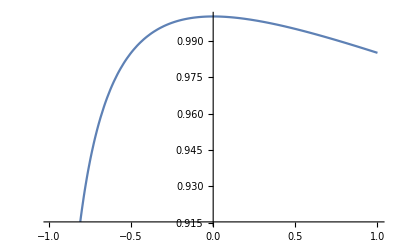

```mathematica
Plot[12*p0000[A[lp[k]], B[1,lp[k], Np], A[lp[k]], B[1,lp[k], Np]], {k,-0.99,1}]
```

```mathematica
p0000[A[lp[0]], B[1,lp[0], Np], A[lp[0]], B[1,lp[0], Np]]
```

1/12